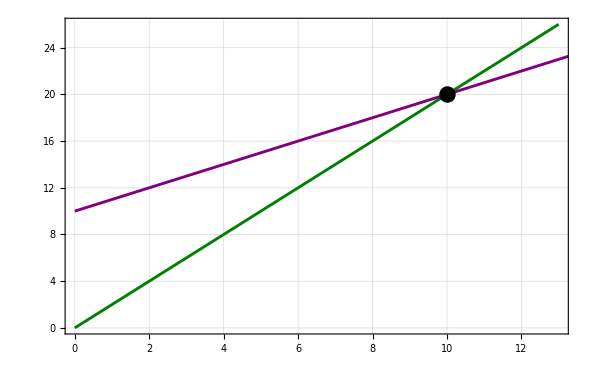

```mathematica
x4=Plot [2x,{x,0,120},PlotStyle->{RGBColor["Green"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,13},{0,26}},PlotLegends->Placed[LineLegend[{RGBColor["Green"]},{Style["x1(t)",20,Black,FontFamily->"Cambria"]}],{0.1,0.8}]];

x5=Plot [10+x,{x,0,120},PlotStyle->{RGBColor["Purple"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,13},{0,26}},PlotLegends->Placed[LineLegend[{RGBColor["Purple"]},{Style["x2(t)",20,Black,FontFamily->"Cambria"]}],{0.1,0.8}]];
intersectionPlot=Graphics[{PointSize[0.02],RGBColor["Black"],Point[{10,20}]}];
Show[x4,x5, intersectionPlot]
```